# Differences between primes

## Visibility definitions

```mathematica
horizontalQ[a_Integer, b_Integer, ts_List]:=Block[{result=True},
	Do[
		If[ts[[x]] < ts[[a]] && ts[[x]] < ts[[b]],result=True,result=False;Return[False]],
		{x,a+1,b-1}
	];
	Return[result]
]
```

```mathematica
visibleQ[a_Integer, b_Integer, ts_List]:=Block[{result=True},
	Do[
		If[ts[[x]] >= ts[[a]]+(ts[[b]]−ts[[a]])(x−a)/(b−a),result=False;Return[]],
		{x,a+1,b-1}
	];
	result
]
```

## Primes

## Create list of primes-n

```mathematica
(*allPrimes = {{1},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}};*)
Do[
divisors=Length@Divisors[x];
If[divisors==9,
AppendTo[allPrimes[[divisors]],x]
],{x,3000000,3500000}]
```

### Shortcut for n odd and prime

```mathematica
primes[n_, l_]:=Table[Prime[x]^(n-1), {x,l}]/;OddQ[n]
```

```mathematica
DumpSave[StringJoin[NotebookDirectory[], "allPrimes.mx"],allPrimes];
```

```mathematica
Get[StringJoin[NotebookDirectory[] , "allPrimes.mx"]]
```

```mathematica
Length/@allPrimes
```

{0,10000,10000,208192,10000,43519,10000,224427,10043,2354638,10000}

```mathematica
allPrimes[[11]]=primes[11,10000];
```

```mathematica
Export[NotebookDirectory[]<>"9-primes.csv", allPrimes[[9]]]
```

/Users/blmayer/doctorate/thesis/article/9-primes.csv

```mathematica
allPrimes=Take[#,UpTo[401]]&/@allPrimes;
```

## Run research

```mathematica
results=Join[
NotebookEvaluate[StringJoin[NotebookDirectory[],"2-primes.nb"]],
NotebookEvaluate[StringJoin[NotebookDirectory[],"3-primes.nb"]],
NotebookEvaluate[StringJoin[NotebookDirectory[],"4-primes.nb"]],
NotebookEvaluate[StringJoin[NotebookDirectory[],"5-primes.nb"]],
NotebookEvaluate[StringJoin[NotebookDirectory[],"6-primes.nb"]]
];
```

```mathematica
TableForm[results, TableHeadings->{None,{"Algorithm","n","len","⟨k⟩","γ","C"}}]
```

Algorithm | n | len | ⟨k⟩ | γ | C
visibility | 2 | 500 | 5.836 | 1.12688 ± 0.220426 | 0.491595 ± 0.14366
horizontal | 2 | 500 | 3.456 | 1.65315 ± 0.449543 | 1.25964 ± 0.550225
visibility | 3 | 500 | 6.776 | 0.984145 ± 0.236521 | 0.37697 ± 0.130101
horizontal | 3 | 500 | 3.844 | 1.54823 ± 0.28404 | 1.05328 ± 0.304314
visibility | 4 | 500 | 6.128 | 1.50648 ± 0.242951 | 1.10629 ± 0.400359
horizontal | 4 | 500 | 3.416 | 1.8667 ± 0.227655 | 1.59138 ± 0.329767
visibility | 5 | 500 | 16.092 | 0.918865 ± 0.115679 | 0.258773 ± 0.0499296
horizontal | 5 | 500 | 3.756 | 1.54544 ± 0.288127 | 1.0632 ± 0.310422
visibility | 6 | 500 | 5.876 | 1.05724 ± 0.296774 | 0.444905 ± 0.182331
horizontal | 6 | 500 | 3.78 | 1.65093 ± 0.192867 | 1.19818 ± 0.225837

```mathematica
{{"horizontal","11",9999,3.946994699469947,"1.57781 ± 0.2041","1.06862 ± 0.222795"}}//TableForm
```

horizontal | 11 | 9999 | 3.94699 | 1.57781 ± 0.2041 | 1.06862 ± 0.222795

```mathematica
{{"visibility","11",9999,45.17231723172317,"0.911266 ± 0.0431205","0.186169 ± 0.0150546"}}//TableForm
```

visibility | 11 | 9999 | 45.1723 | 0.911266 ± 0.0431205 | 0.186169 ± 0.0150546

## Graphics

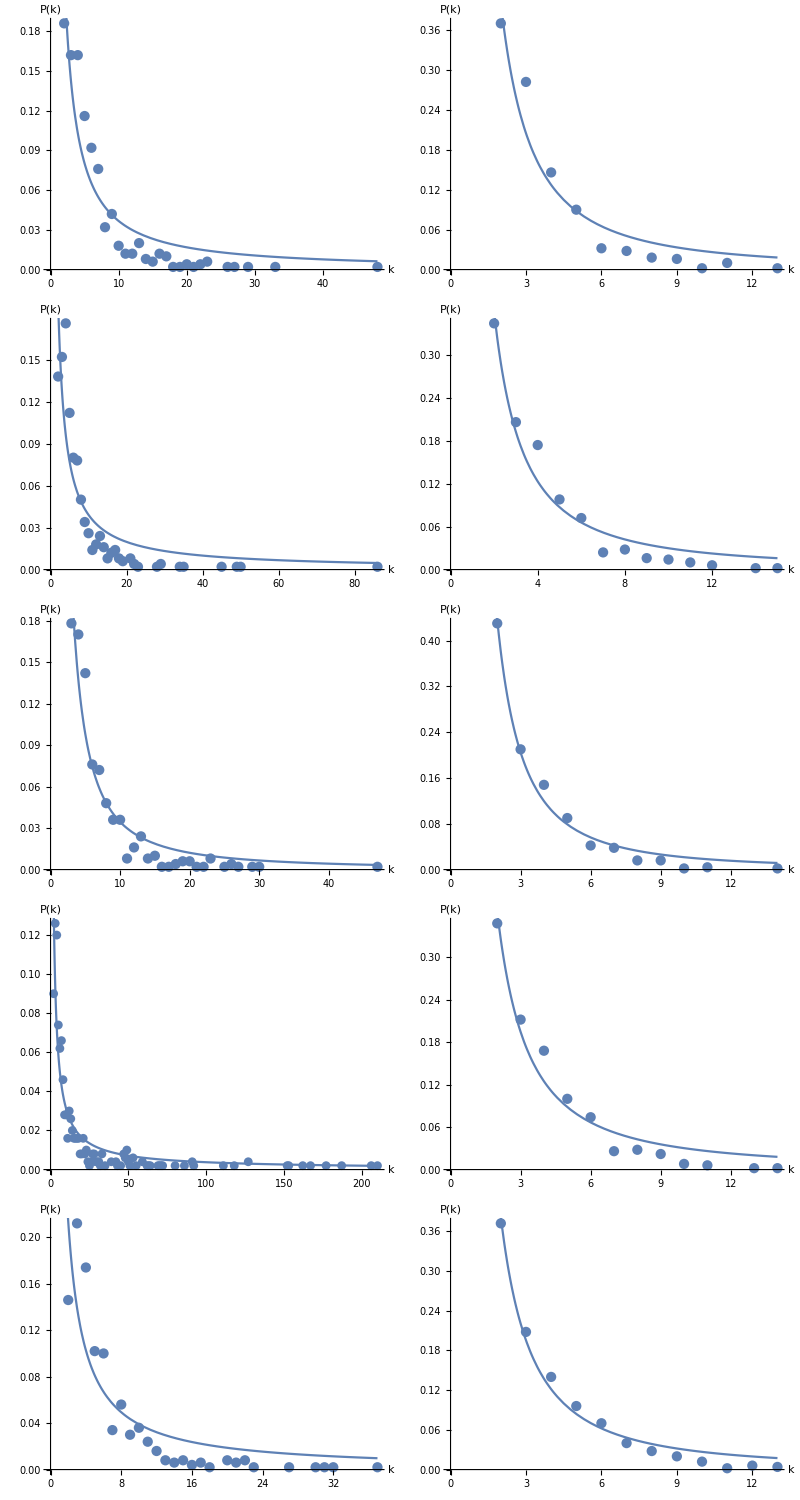

```mathematica
frame=Grid[
Map[Show[#,ImageSize-> Large]&,{{vis2,hvis2},{vis3,hvis3},{vis4,hvis4},{vis5,hvis5},{vis6,hvis6}},{2}]]
```

```mathematica
Export[NotebookDirectory[]<>"frame.eps",frame]
```

/Users/blmayer/doctorate/thesis/article/frame.eps

```mathematica
Export[NotebookDirectory[]<>"vis2.eps",vis2];
Export[NotebookDirectory[]<>"hvis2.eps",hvis2];
Export[NotebookDirectory[]<>"vis3.eps",vis3];
Export[NotebookDirectory[]<>"hvis3.eps",hvis3];
Export[NotebookDirectory[]<>"vis4.eps",vis4];
Export[NotebookDirectory[]<>"hvis4.eps",hvis4];
Export[NotebookDirectory[]<>"vis5.eps",vis5];
Export[NotebookDirectory[]<>"hvis5.eps",hvis5];
Export[NotebookDirectory[]<>"vis6.eps",vis6];
Export[NotebookDirectory[]<>"hvis6.eps",hvis6];
```

## Grid of graphs

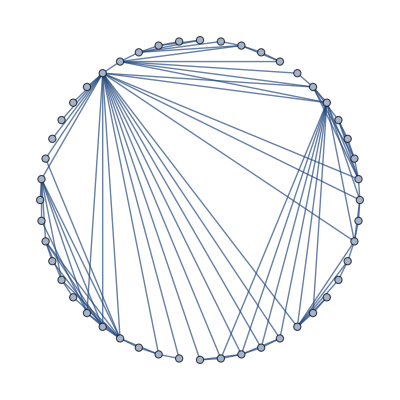
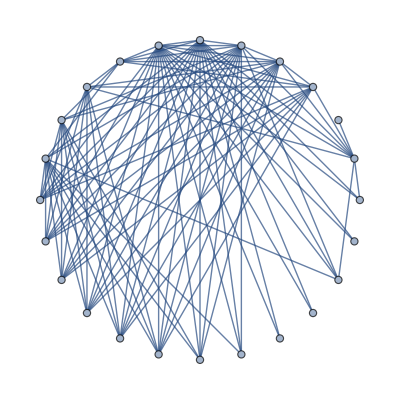
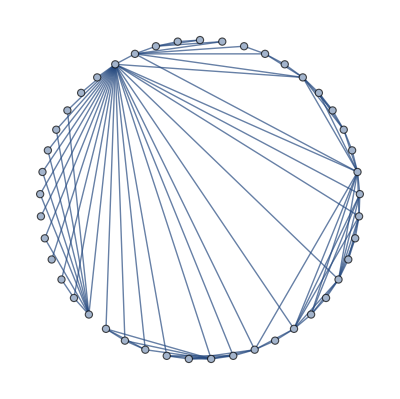
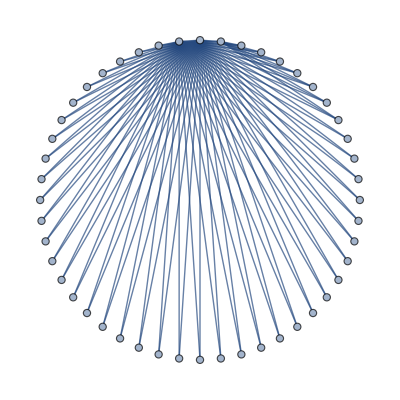
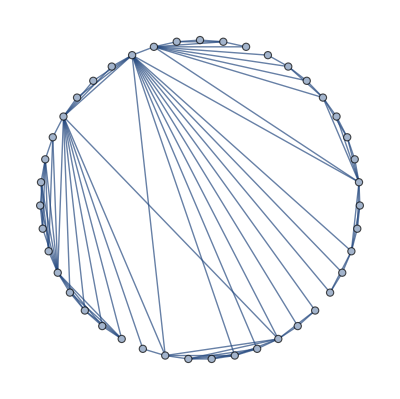
-Graphics-d=2 | -Graphics-d=3
-Graphics-d=4 | -Graphics-d=5
-Graphics-d=6 |

```mathematica
frame=Grid[Map[#&,{{gv2, gv3},{gv4, gv5}, {gv6}},{2}]]
```

```mathematica
Export[NotebookDirectory[]<>"graphs.eps", frame]
```

/Users/blmayer/doctorate/thesis/article/graphs.eps

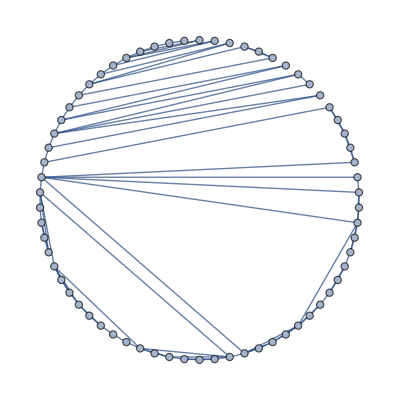
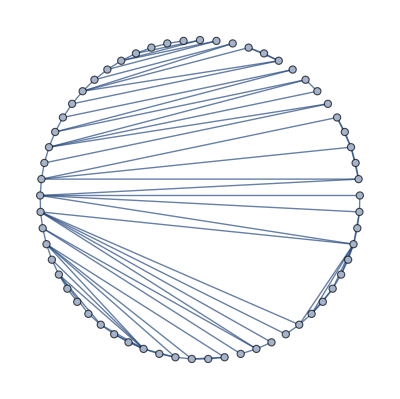
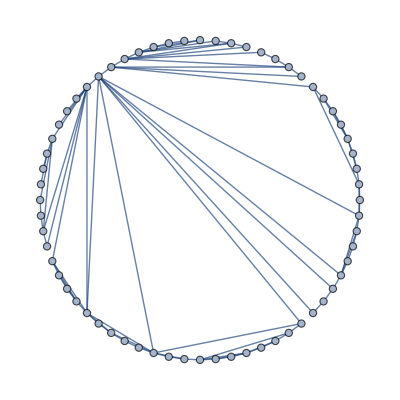
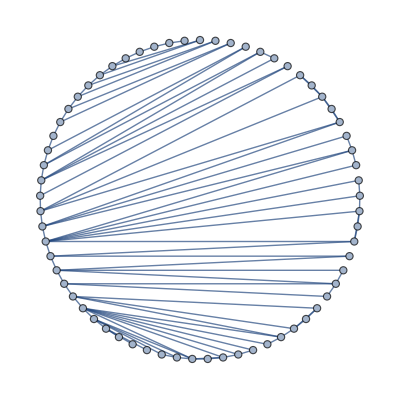
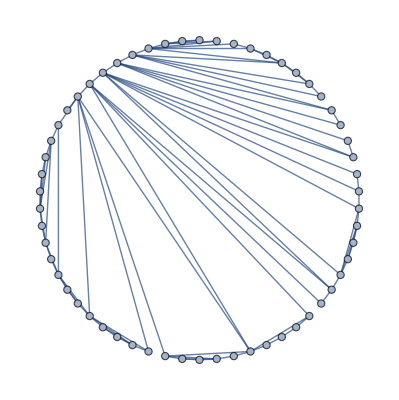
-Graphics-d=2 | -Graphics-d=3
-Graphics-d=4 | -Graphics-d=5
-Graphics-d=6 |

```mathematica
hframe=Grid[Map[#&,{{gh2, gh3},{gh4, gh5},{gh6}},{2}]]
```

```mathematica
Export[NotebookDirectory[]<>"hgraphs.eps", hframe]
```

/Users/blmayer/doctorate/thesis/article/hgraphs.eps